```mathematica
Quit[]
```

```mathematica
ρ[t]/.solsqy/.t->100//MatrixForm
```

((0.110622+2.2003×10^-20 ⅈ
-0.000249447+0.119591 ⅈ
-0.000249447+0.119591 ⅈ
-0.239149-2.45864×10^-20 ⅈ) | (-0.000249447-0.119591 ⅈ
0.184754+4.96623×10^-19 ⅈ
0.18425-8.17013×10^-19 ⅈ
0.000539791+0.258789 ⅈ) | (-0.000249447-0.119591 ⅈ
0.18425+1.20723×10^-18 ⅈ
0.184754+5.47414×10^-20 ⅈ
0.000539791+0.258789 ⅈ) | (-0.239149-2.45864×10^-20 ⅈ
0.000539791-0.258789 ⅈ
0.000539791-0.258789 ⅈ
0.519869+3.83497×10^-19 ⅈ))

```mathematica
N[Sinh[rr]^2/(2Sinh[rr]^2+1)]
```

0.175973

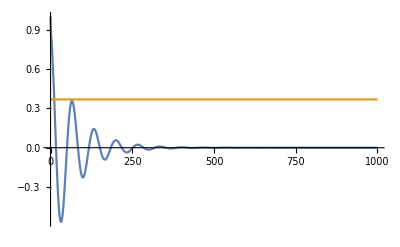

```mathematica
Plot[{Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]],1/E},{t,0,1000}]
```

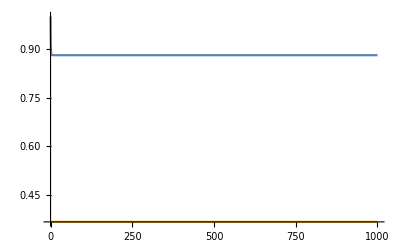

```mathematica
Plot[{Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]],1/E},{t,0,100}]
```

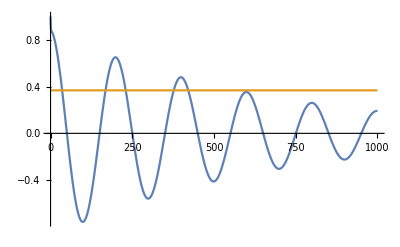

```mathematica
Plot[{Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]],1/E},{t,0,1000}]
```

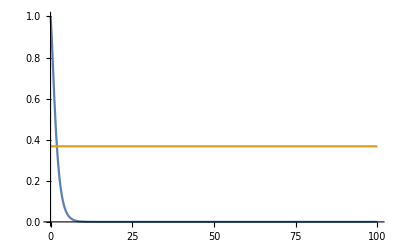

```mathematica
Plot[{Re[Evaluate[a[1,3][t]/.solsqx]+Evaluate[a[2,4][t]/.solsqx]+Evaluate[a[3,1][t]/.solsqx]+Evaluate[a[4,2][t]/.solsqx]][[1]],1/E},{t,0,100}]
```

```mathematica
di=0.51 λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;
γp12=1;γp21=1;γp11=γ12 ;
γp22=γ12 ;
solsqy=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==inity,WhenEvent[Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]]<1/E ,dy=1/t]},slnn,{t,0,10000},MaxSteps->50000];
1/dy
```

WhenEvent::nonopt: Options expected (instead of StopIntegration) beyond position 2 in WhenEvent[Im[-Evaluate[ReplaceAll[«2»]]-Evaluate[ReplaceAll[«2»]]+Evaluate[a[«2»][«1»]/.solsqy]+Evaluate[a[«2»][«1»]/.solsqy]]⟦1⟧<1/ⅇ,dy=1/t,StopIntegration]. An option must be a rule or a list of rules.

421.147

```mathematica
x
```

0.51

```mathematica
Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqy=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==inity,WhenEvent[Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]]<1/E ,dy=1/t]},slnn,{t,0,10000},MaxSteps->50000];dy},{n,0.45,0.55,0.01}]
```

{{0.45,0.152239},{0.46,0.119647},{0.47,0.0880535},{0.48,0.00907969},{0.49,0.00237447},{0.5,0.00237447},{0.51,0.00237447},{0.52,0.00907969},{0.53,0.0880535},{0.54,0.119647},{0.55,0.152239}}

```mathematica
σ[1,1]=({{0, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});(*|e1><g1|*)σ[1,0]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}});(*|g1><e1|*)
σ[2,1]=({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}});(*|e2><g2|*)σ[2,0]=({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}});(*|g2><e2|*)
ρ[t_]:=Table[a[i,j][t],{i,4},{j,4}]
slnn=Flatten[Table[a[i,j][t],{i,4},{j,4}]]; Λp12= Λp21=0;
Λ12= Λ21;
```

```mathematica
γ[1,1]=γ[2,2]=γ;
γs[1,1]=γs[2,2]=γ;
γ[1,2]=γ12;γ[2,1]=γ12;
γs[1,2]=γ21;γs[2,1]=γ21;
γp[1,1]=γp11 ;γp[2,2]=γp22;
γps[1,1]=γp11 ;γps[2,2]=γp22;
γp[1,2]=γp12;γp[2,1]=γp21;
γps[1,2]=γp21;γps[2,1]=γp12;
SQ=-1/2sh ch(Sum[γp[i,j]Exp[I α](ρ[t].σ[i,1].σ[j,1]+σ[i,1].σ[j,1].ρ[t]-σ[i,1].ρ[t].σ[j,1]-σ[j,1].ρ[t].σ[i,1])+γps[i,j]Exp[-I α](ρ[t].σ[j,0].σ[i,0]+σ[j,0].σ[i,0].ρ[t]-σ[j,0].ρ[t].σ[i,0]-σ[i,0].ρ[t].σ[j,0]),{i,1,2},{j,1,2}])-1/2(sh^2+1)Sum[γ[i,j](σ[i,1].σ[j,0].ρ[t]-σ[j,0].ρ[t].σ[i,1])+γs[i,j](ρ[t].σ[j,1].σ[i,0]-σ[i,0].ρ[t].σ[j,1]),{i,1,2},{j,1,2}]-1/2sh^2Sum[γ[i,j](ρ[t].σ[j,0].σ[i,1]-σ[i,1].ρ[t].σ[j,0])+γs[i,j](σ[i,0].σ[j,1].ρ[t]-σ[j,1].ρ[t].σ[i,0]),{i,1,2},{j,1,2}];
```

```mathematica
Solve[{ee== a[1,1][t],gg== a[4,4][t],pp==1/2(a[2,2][t]+a[2,3][t]+a[3,2][t]+a[3,3][t]),mm==1/2(a[2,2][t]-a[2,3][t]-a[3,2][t]+a[3,3][t])},{a[1,1][t]}]
```

```mathematica
Collect[SQ[[1,1]],sh ch]
```

-2 (1+sh^2) γ a[1,1][t]-1/2 sh^2 (-2 γ a[2,2][t]-γ12 a[2,3][t]-γ21 a[2,3][t]-γ12 a[3,2][t]-γ21 a[3,2][t]-2 γ a[3,3][t])+1/2 ch sh (-ⅇ^(-ⅈ α) γp12 a[1,4][t]-ⅇ^(-ⅈ α) γp21 a[1,4][t]-ⅇ^(ⅈ α) γp12 a[4,1][t]-ⅇ^(ⅈ α) γp21 a[4,1][t])

```mathematica
Collect[(SQ[[2,2]]+ SQ[[2,3]]+SQ[[3,2]]+SQ[[3,3]])/2,sh ch]
```

1/2 ch sh (ⅇ^(-ⅈ α) γp12 a[1,4][t]+ⅇ^(-ⅈ α) γp21 a[1,4][t]+ⅇ^(ⅈ α) γp12 a[4,1][t]+ⅇ^(ⅈ α) γp21 a[4,1][t]+1/2 (2 ⅇ^(-ⅈ α) γp22 a[1,4][t]+2 ⅇ^(ⅈ α) γp11 a[4,1][t])+1/2 (2 ⅇ^(-ⅈ α) γp11 a[1,4][t]+2 ⅇ^(ⅈ α) γp22 a[4,1][t]))+1/2 (-1/2 (1+sh^2) (-2 γ a[1,1][t]+2 γ a[2,2][t]+γ21 a[2,3][t]+γ12 a[3,2][t])-1/2 (1+sh^2) (-2 γ a[1,1][t]+γ12 a[2,3][t]+γ21 a[3,2][t]+2 γ a[3,3][t])-1/2 (1+sh^2) (γ21 (-a[1,1][t]+a[2,2][t])+2 γ a[2,3][t]+γ12 (-a[1,1][t]+a[3,3][t]))-1/2 (1+sh^2) (γ12 (-a[1,1][t]+a[2,2][t])+2 γ a[3,2][t]+γ21 (-a[1,1][t]+a[3,3][t]))-1/2 sh^2 (2 γ a[3,2][t]+γ21 (a[2,2][t]-a[4,4][t])+γ12 (a[3,3][t]-a[4,4][t]))-1/2 sh^2 (2 γ a[2,3][t]+γ12 (a[2,2][t]-a[4,4][t])+γ21 (a[3,3][t]-a[4,4][t]))-1/2 sh^2 (2 γ a[2,2][t]+γ12 a[2,3][t]+γ21 a[3,2][t]-2 γ a[4,4][t])-1/2 sh^2 (γ21 a[2,3][t]+γ12 a[3,2][t]+2 γ a[3,3][t]-2 γ a[4,4][t]))

```mathematica
Collect[1/4 ch ⅇ^(-ⅈ α) sh (2 (γp11+γp12+γp21+γp22) a[1,4][t]+2 ⅇ^(2 ⅈ α) γp11 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp12 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp21 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp22 a[4,1][t]),{a[1,4][t],a[4,1][t]}]
```

1/2 ch ⅇ^(-ⅈ α) sh (γp11+γp12+γp21+γp22) a[1,4][t]+1/4 ch ⅇ^(-ⅈ α) sh (2 ⅇ^(2 ⅈ α) γp11+2 ⅇ^(2 ⅈ α) γp12+2 ⅇ^(2 ⅈ α) γp21+2 ⅇ^(2 ⅈ α) γp22) a[4,1][t]

```mathematica
Collect[(SQ[[2,2]]- SQ[[2,3]]-SQ[[3,2]]+SQ[[3,3]])/2,sh ch]
```

1/2 ch sh (ⅇ^(-ⅈ α) γp12 a[1,4][t]+ⅇ^(-ⅈ α) γp21 a[1,4][t]+ⅇ^(ⅈ α) γp12 a[4,1][t]+ⅇ^(ⅈ α) γp21 a[4,1][t]+1/2 (-2 ⅇ^(-ⅈ α) γp22 a[1,4][t]-2 ⅇ^(ⅈ α) γp11 a[4,1][t])+1/2 (-2 ⅇ^(-ⅈ α) γp11 a[1,4][t]-2 ⅇ^(ⅈ α) γp22 a[4,1][t]))+1/2 (-1/2 (1+sh^2) (-2 γ a[1,1][t]+2 γ a[2,2][t]+γ21 a[2,3][t]+γ12 a[3,2][t])-1/2 (1+sh^2) (-2 γ a[1,1][t]+γ12 a[2,3][t]+γ21 a[3,2][t]+2 γ a[3,3][t])+1/2 (1+sh^2) (γ21 (-a[1,1][t]+a[2,2][t])+2 γ a[2,3][t]+γ12 (-a[1,1][t]+a[3,3][t]))+1/2 (1+sh^2) (γ12 (-a[1,1][t]+a[2,2][t])+2 γ a[3,2][t]+γ21 (-a[1,1][t]+a[3,3][t]))+1/2 sh^2 (2 γ a[3,2][t]+γ21 (a[2,2][t]-a[4,4][t])+γ12 (a[3,3][t]-a[4,4][t]))+1/2 sh^2 (2 γ a[2,3][t]+γ12 (a[2,2][t]-a[4,4][t])+γ21 (a[3,3][t]-a[4,4][t]))-1/2 sh^2 (2 γ a[2,2][t]+γ12 a[2,3][t]+γ21 a[3,2][t]-2 γ a[4,4][t])-1/2 sh^2 (γ21 a[2,3][t]+γ12 a[3,2][t]+2 γ a[3,3][t]-2 γ a[4,4][t]))

```mathematica
Collect[1/4 ch ⅇ^(-ⅈ α) sh (-2 (γp11-γp12-γp21+γp22) a[1,4][t]-2 ⅇ^(2 ⅈ α) γp11 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp12 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp21 a[4,1][t]-2 ⅇ^(2 ⅈ α) γp22 a[4,1][t]),{a[1,4][t],a[4,1][t]}]
```

-1/2 ch ⅇ^(-ⅈ α) sh (γp11-γp12-γp21+γp22) a[1,4][t]+1/4 ch ⅇ^(-ⅈ α) sh (-2 ⅇ^(2 ⅈ α) γp11+2 ⅇ^(2 ⅈ α) γp12+2 ⅇ^(2 ⅈ α) γp21-2 ⅇ^(2 ⅈ α) γp22) a[4,1][t]

```mathematica
Collect[Simplify[(SQ[[1,1]]- SQ[[4,1]]-SQ[[1,4]]+SQ[[4,4]])/2],sh ch]
```

1/4 (-4 (1+sh^2) γ a[1,1][t]+2 sh^2 γ a[1,4][t]+2 (1+sh^2) γ a[1,4][t]+sh^2 (2 γ a[2,2][t]+(γ12+γ21) a[2,3][t]+γ12 a[3,2][t]+γ21 a[3,2][t]+2 γ a[3,3][t])+(1+sh^2) (2 γ a[2,2][t]+(γ12+γ21) a[2,3][t]+γ12 a[3,2][t]+γ21 a[3,2][t]+2 γ a[3,3][t])+2 sh^2 γ a[4,1][t]+2 (1+sh^2) γ a[4,1][t]-4 sh^2 γ a[4,4][t])+1/4 ch sh (-2 ⅇ^(-ⅈ α) (γp12+γp21) (a[1,4][t]+ⅇ^(2 ⅈ α) a[4,1][t])+ⅇ^(ⅈ α) ((γp12+γp21) a[1,1][t]-(γp12+γp21) a[2,2][t]-2 γp22 a[2,3][t]-2 γp11 a[3,2][t]-γp12 a[3,3][t]-γp21 a[3,3][t]+γp12 a[4,4][t]+γp21 a[4,4][t])+ⅇ^(-ⅈ α) ((γp12+γp21) a[1,1][t]-(γp12+γp21) a[2,2][t]-2 γp11 a[2,3][t]-2 γp22 a[3,2][t]-γp12 a[3,3][t]-γp21 a[3,3][t]+γp12 a[4,4][t]+γp21 a[4,4][t]))

```mathematica
Collect[1/4 ch ⅇ^(-ⅈ α) sh (-2 (γp11-γp12-γp21+γp22) a[1,4][t]-2 ⅇ^(2 ⅈ α) γp11 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp12 a[4,1][t]+2 ⅇ^(2 ⅈ α) γp21 a[4,1][t]-2 ⅇ^(2 ⅈ α) γp22 a[4,1][t]),{a[1,4][t],a[4,1][t]}]
```

```mathematica
Collect[ⅇ^(-ⅈ α)SQ[[1,4]]+ⅇ^(ⅈ α)SQ[[4,1]],sh ch]
```

-ⅇ^(-ⅈ α) sh^2 γ a[1,4][t]-ⅇ^(-ⅈ α) (1+sh^2) γ a[1,4][t]-ⅇ^(ⅈ α) sh^2 γ a[4,1][t]-ⅇ^(ⅈ α) (1+sh^2) γ a[4,1][t]+ch sh (-1/2 ⅇ^(ⅈ α) (-2 ⅇ^(-ⅈ α) γp11 a[2,3][t]-2 ⅇ^(-ⅈ α) γp22 a[3,2][t]+ⅇ^(-ⅈ α) γp12 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t])+ⅇ^(-ⅈ α) γp21 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t]))-1/2 ⅇ^(-ⅈ α) (-2 ⅇ^(ⅈ α) γp22 a[2,3][t]-2 ⅇ^(ⅈ α) γp11 a[3,2][t]+ⅇ^(ⅈ α) γp12 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t])+ⅇ^(ⅈ α) γp21 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t])))

```mathematica
Collect[ch sh (-1/2 ⅇ^(ⅈ α) ((γp12+γp21) a[1,1][t]-(γp12+γp21) a[2,2][t]-2 γp22 a[2,3][t]-2 γp11 a[3,2][t]-γp12 a[3,3][t]-γp21 a[3,3][t]+γp12 a[4,4][t]+γp21 a[4,4][t])+1/2 (2 ⅇ^(-ⅈ α) γp11 a[2,3][t]+2 ⅇ^(-ⅈ α) γp22 a[3,2][t]-ⅇ^(-ⅈ α) γp12 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t])-ⅇ^(-ⅈ α) γp21 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t]))),{a[1,4][t],a[4,1][t]}]
```

ch sh (-1/2 ⅇ^(ⅈ α) ((γp12+γp21) a[1,1][t]-(γp12+γp21) a[2,2][t]-2 γp22 a[2,3][t]-2 γp11 a[3,2][t]-γp12 a[3,3][t]-γp21 a[3,3][t]+γp12 a[4,4][t]+γp21 a[4,4][t])+1/2 (2 ⅇ^(-ⅈ α) γp11 a[2,3][t]+2 ⅇ^(-ⅈ α) γp22 a[3,2][t]-ⅇ^(-ⅈ α) γp12 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t])-ⅇ^(-ⅈ α) γp21 (a[1,1][t]-a[2,2][t]-a[3,3][t]+a[4,4][t])))

```mathematica
Quit[]
```

```mathematica
γ11=1;γ12=Cos[r2-r1];γp11=Cos[2r1];γp22=Cos[2r2];γp21=γp12=Cos[(r1+r2)];
```

```mathematica
Z=Solve[{-2(n+1)γ11 ee+n((γ11+γ12)ss+(γ11-γ12)aa)-γp12 √(n(n+1)) u==0,(γ11+γ12)(n-(3n+1)ss-n aa+ee)+1/2(γp11+2γp12+γp22)√(n(n+1)) u==0,(γ11-γ12)(n-(3n+1)aa-n ss+ee)+1/2(-γp11+2γp12-γp22)√(n(n+1)) u==0,-2γp12 √(n(n+1))-(2n+1)γ11 u+√(n(n+1))((4γp12+γp11+γp22)ss+(4γp12-γp11-γp22)aa)==0},{ee,ss,aa,u}]//Simplify
```

{{ee→(n (-1-n-2 n^2+(-1+n+2 n^2) Cos[2 (r1+r2)]))/(2 (1+2 n) (-1-2 n-2 n^2+2 n (1+n) Cos[2 (r1+r2)])),ss→-(n (1+n) Sin[r1+r2]^2)/(-1-2 n-2 n^2+2 n (1+n) Cos[2 (r1+r2)]),aa→-(n (1+n) Sin[r1+r2]^2)/(-1-2 n-2 n^2+2 n (1+n) Cos[2 (r1+r2)]),u→(2 √(n (1+n)) Cos[r1+r2])/((1+2 n) (-1-2 n-2 n^2+2 n (1+n) Cos[2 (r1+r2)]))}}

```mathematica
γ11=1;γ12=0;γp11=0;γp22=0;γp21=γp12=Cos[(r1+r2)];Z=Solve[{-2(n+1)γ11 ee+n((γ11+γ12)ss+(γ11-γ12)aa)-γp12 √(n(n+1)) u==0,(γ11+γ12)(n-(3n+1)ss-n aa+ee)+1/2(γp11+2γp12+γp22)√(n(n+1)) u==0,(γ11-γ12)(n-(3n+1)aa-n ss+ee)+1/2(-γp11+2γp12-γp22)√(n(n+1)) u==0,-2γp12 √(n(n+1))-(2n+1)γ11 u+√(n(n+1))((4γp12+γp11+γp22)ss+(4γp12-γp11-γp22)aa)==0},{ee,ss,aa,u}]//Simplify
```

{{ee→(n (-n (1+2 n)+(-1+n+2 n^2) Cos[r1+r2]^2))/((1+2 n) (-(1+2 n)^2+4 n (1+n) Cos[r1+r2]^2)),ss→-(n (1+n) Sin[r1+r2]^2)/(-1-2 n-2 n^2+2 n (1+n) Cos[2 (r1+r2)]),aa→-(n (1+n) Sin[r1+r2]^2)/(-1-2 n-2 n^2+2 n (1+n) Cos[2 (r1+r2)]),u→(2 √(n (1+n)) Cos[r1+r2])/((1+2 n) (-(1+2 n)^2+4 n (1+n) Cos[r1+r2]^2))}}